## Write Data to files. CPL

Preparing

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica

Test Legend fuctioning.

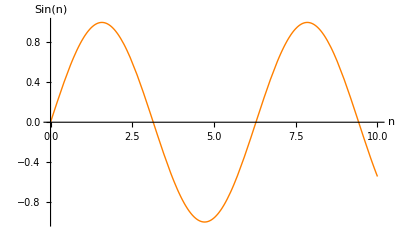

```mathematica
(*********************************************)
Print[Style["Preparing",30,Bold,Orange]]
(*********************************************)
Needs["PlotLegends`"]
SetDirectory["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\"]
(*********************************************)
(*Manually set the start point(a<1) of this table.*)
(*
tranzs=31 ;tranzDE2=29;tranzDE3=23;tranzDE4=23;tranzL=23;
*)
(*Manually set the criteria for the element in aokTabL etc that corresponds to normalization time.*)
(*
norts=138-tranzs;nortL=138-tranzL;nort2=138-tranzDE2;nort3=138-tranzDE4;nort4=138-tranzDE4;
nort=138-tranzL;
*)
(**************************)
Print[Style["Test Legend fuctioning.",30,Bold,Orange]]
Plot[Sin[n],{n,0,10},PlotStyle->Orange,AxesLabel-> {"n","Sin(n)"},PlotLegend->{"Sin"},LegendPosition->{1.1,-0.4}]
```

```mathematica
(********)
Print[Style["Parameters",Orange]]
(*********)
wL=-1;
wCPL[a_]:=w0+wa (1-a);
w20=-1;
w2a=0.1;
w30=-1;
w3a=-0.1;
w40=-0.9;
w4a=-0.1;
w50=-0.9;
w5a=0.1;
w60=-0.9;
w6a=-0.2;
ΩDE0=0.734;
Ωk0=0;
Ωm0=0.1334/(0.71^2);
Ωr0=8.09*10^-5;
h=0.71;
H0=(100 h)/300000 ;
Ωm0s=1;Ωr0s=8.09*10^-5;
(********)
Print[Style["Set the Hubble constant the same at Equality",Orange]]
(*********)
aes=Ωr0s/Ωm0s
aeq=Ωr0/Ωm0
HL0=H0;
Hs0=(HL0 √(Ωm0 aeq^-3+Ωr0 aeq^-4+ΩDE0 aeq^(-3(1+wL))))/(√(Ωm0s aes^-3+Ωr0s aes^-4))
H20=(HL0 √(Ωm0 aeq^-3+Ωr0 aeq^-4+ΩDE0 aeq^(-3(1+wL))))/(√(Ωm0 aeq^-3+Ωr0 aeq^-4+ΩDE0 aeq^(-3(1+w20+w2a))Exp[-3  w2a (1-aeq)]))
H30=(HL0 √(Ωm0 aeq^-3+Ωr0 aeq^-4+ΩDE0 aeq^(-3(1+wL))))/(√(Ωm0 aeq^-3+Ωr0 aeq^-4+ΩDE0 aeq^(-3(1+w30+w3a))Exp[-3  w3a (1-aeq)]))
H40=(HL0 √(Ωm0 aeq^-3+Ωr0 aeq^-4+ΩDE0 aeq^(-3(1+wL))))/(√(Ωm0 aeq^-3+Ωr0 aeq^-4+ΩDE0 aeq^(-3(1+w40+w4a))Exp[-3  w4a (1-aeq)]))
H50=(HL0 √(Ωm0 aeq^-3+Ωr0 aeq^-4+ΩDE0 aeq^(-3(1+wL))))/(√(Ωm0 aeq^-3+Ωr0 aeq^-4+ΩDE0 aeq^(-3(1+w50+w5a))Exp[-3  w5a (1-aeq)]))
H60=(HL0 √(Ωm0 aeq^-3+Ωr0 aeq^-4+ΩDE0 aeq^(-3(1+wL))))/(√(Ωm0 aeq^-3+Ωr0 aeq^-4+ΩDE0 aeq^(-3(1+w60+w6a))Exp[-3  w6a (1-aeq)]))
(********)
Print[Style["Hubble functions",Orange]]
(*********)
Hs[a_]=Hs0 √(Ωm0s a^-3+Ωr0s a^-4)
HL[a_]=HL0  √(Ωm0 a^-3+Ωr0 a^-4+ΩDE0 a^(-3(1+wL)))
H2[a_]=H20  √(Ωm0 a^-3+Ωr0 a^-4+ΩDE0 a^(-3(1+w20+w2a))Exp[-3  w2a (1-a)])
H3[a_]=H30 √(Ωm0 a^-3+Ωr0 a^-4+ΩDE0 a^(-3(1+w30+w3a))Exp[-3  w3a (1-a)])
H4[a_]=H40 √(Ωm0 a^-3+Ωr0 a^-4+ΩDE0 a^(-3(1+w40+w4a))Exp[-3  w4a (1-a)])
H5[a_]=H50 √(Ωm0 a^-3+Ωr0 a^-4+ΩDE0 a^(-3(1+w50+w5a))Exp[-3  w5a (1-a)])
H6[a_]=H60 √(Ωm0 a^-3+Ωr0 a^-4+ΩDE0 a^(-3(1+w60+w6a))Exp[-3  w6a (1-a)])
(********)
Print[Style["Define the wave number",Orange]]
(*********)
ks[a_]=Hs[a];kL[a_]=HL[a];kDE2[a_]=H2[a];kDE3[a_]=H3[a];kDE4[a_]=H4[a];kDE5[a_]=H5[a];kDE6[a_]=H6[a];
(*ss[k_]:=NSolve[k==Subscript[H, 1][Subscript[a, 1]]&&Subscript[a, 1]>0,Subscript[a, 1]]//FullSimplify
Solve[k==Subscript[H, 2][Subscript[a, 2]],Subscript[a, 2]];*)
(********)
Print[Style["Define the growth factors",Orange]]
(*********)
Growths[a_]= 5/2 Ωm0s  Hs[a]/H0  NIntegrate[1/(x^3(Hs[x]/H0)^3),{x,0,a}];
GrowthL[a_]= 5/2 Ωm0  HL[a]/H0  NIntegrate[1/(x^3(HL[x]/H0)^3),{x,0,a}];
GrowthDE2[a_]=5/2 Ωm0 H2[a]/H0  NIntegrate[1/(x^3(H2[x]/H0)^3),{x,0,a}];
GrowthDE3[a_]=5/2 Ωm0 H3[a]/H0  NIntegrate[1/(x^3(H3[x]/H0)^3),{x,0,a}];
GrowthDE4[a_]=5/2 Ωm0 H4[a]/H0  NIntegrate[1/(x^3(H4[x]/H0)^3),{x,0,a}];
GrowthDE5[a_]=5/2 Ωm0 H5[a]/H0  NIntegrate[1/(x^3(H5[x]/H0)^3),{x,0,a}];
GrowthDE6[a_]=5/2 Ωm0 H6[a]/H0  NIntegrate[1/(x^3(H6[x]/H0)^3),{x,0,a}];
(********)
Print[Style["Plots for the wave numbers",Orange]]
(********)
LogPlot[{ks[a],kL[a],kDE2[a],H3[a],H4[a],H5[a],H6[a]},{a,10^-4,1},PlotStyle->{Red,Orange,Yellow,Green,Blue,Cyan,Purple}]
LogLogPlot[{ks[a],kL[a],kDE2[a],H3[a],H4[a],H5[a],H6[a]},{a,10^-4,1},PlotStyle->{Red,Orange,Yellow,Green,Blue,Cyan,Purple}]
LogLinearPlot[{ks[a],kL[a],kDE2[a],H3[a],H4[a],H5[a],H6[a]},{a,10^-4,1},PlotStyle->{Red,Orange,Yellow,Green,Blue,Cyan,Purple}]
(********)
Print[Style["Growth factors vs k | examples",Orange]]
(*********)
ParametricPlot[{Log[kL[a]],Log[GrowthL[1]/GrowthL[a]]},{a,10^-3,1},PlotRange->Full,AxesOrigin-> {-9,0},PlotStyle->{Orange}]
ParametricPlot[{Log[kDE2[a]],Log[GrowthDE2[1]/GrowthDE2[a]]},{a,10^-3,1},PlotRange-> Full, AxesOrigin-> {-9,0},PlotStyle->{Yellow}]
(********)
Print[Style["Growth factors vs a",Orange]]
(*********)
Plot[{Growths[a],GrowthL[a],GrowthDE2[a],GrowthDE3[a],GrowthDE4[a],GrowthDE5[a],GrowthDE6[a]},{a,0,1},PlotStyle->{Red,Orange,Yellow,Green,Blue,Cyan,Purple},AxesLabel-> {a,"D_+(a)"}]
LogLogPlot[{Growths[a],GrowthL[a],GrowthDE2[a]},{a,10^-4,1},PlotStyle->{Red,Orange,Yellow},AxesLabel-> {a,"D_+(a)"}]
(********)
Print[Style["Growth factors with respect to 1+z",Orange]]
(*********)
GL[mn_]:=GrowthL[1/mn];GS[mn_]:=Growths[1/mn];GDE2[mn_]:=GrowthDE2[1/mn];GDE3[mn_]:=GrowthDE3[1/mn];GDE4[mn_]:=GrowthDE4[1/mn];GDE5[mn_]:=GrowthDE5[1/mn];GDE6[mn_]:=GrowthDE6[1/mn];
Lambdas[mn_]=1/Hs[1/mn];LambdaL[mn_]=1/HL[1/mn];Lambda2[mn_]=1/H2[1/mn];Lambda3[mn_]=1/H3[1/mn];Lambda4[mn_]=1/H4[1/mn];Lambda5[mn_]=1/H5[1/mn];Lambda6[mn_]=1/H6[1/mn];
(*LogLogPlot[{GL[mn]/GS[mn], (Subscript[GDE, 2][mn])/GS[mn], (Subscript[GDE, 3][mn])/GS[mn], (Subscript[GDE, 4][mn])/GS[mn], (Subscript[GDE, 5][mn])/GS[mn], (Subscript[GDE, 6][mn])/GS[mn]},{mn,0.1,100},PlotStyle->{Orange,Yellow,Green,Blue,Cyan,Purple},AxesLabel-> {"1+z","D_+(z)(1+z)"},PlotRange->Full,PlotLabel->Growth[1+z]]*)
(********)
Print[Style["Growth factors with respect to 1+z in terms of sCDM",Orange]]
(*********)
LogLogPlot[{(mn)GS[mn],(mn)GL[mn],(mn) GDE2[mn],(mn) GDE3[mn],(mn) GDE4[mn],(mn) GDE5[mn],(mn) GDE6[mn]},{mn,0.1,100},PlotStyle->{Red,Orange,Yellow,Green,Blue,Cyan,Purple},PlotRange->{{1,100},{0.68,1.05}},AxesLabel-> {"1+z","D_+(z)(1+z)"}]
LogLogPlot[{(mn)GS[mn],(mn)GL[mn],(mn) GDE2[mn],(mn) GDE3[mn],(mn) GDE4[mn],(mn) GDE5[mn],(mn) GDE6[mn]},{mn,0.1,100},PlotStyle->{Red,Orange,Yellow,Green,Blue,Cyan,Purple},PlotRange->{{1,10},{0.69,1}},AxesLabel-> {"1+z","D_+(z)(1+z)"}]
(********)
Print[Style["Hubble distances with respect to 1+z",Orange]]
(*********)
(* (*Too ugly*)
LogPlot[{(Subscript[Lambda, L][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 2][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 3][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 4][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 5][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 6][mn])/(Subscript[Lambda, s][mn])},{mn,10^-2,100},PlotStyle->{Orange,Yellow,Green,Blue,Cyan,Purple},AxesLabel->{"1+z","d_H"}]
LogLogPlot[{(Subscript[Lambda, L][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 2][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 3][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 4][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 5][mn])/(Subscript[Lambda, s][mn]),(Subscript[Lambda, 6][mn])/(Subscript[Lambda, s][mn])},{mn,10^-2,100},PlotStyle->{Orange,Yellow,Green,Blue,Cyan,Purple},AxesLabel->{"1+z","d_H"}]
*)
LogLinearPlot[{LambdaL[mn]/Lambdas[mn],Lambda2[mn]/Lambdas[mn],Lambda3[mn]/Lambdas[mn],Lambda4[mn]/Lambdas[mn],Lambda5[mn]/Lambdas[mn],Lambda6[mn]/Lambdas[mn]},{mn,1,100},PlotRange->{{1,110},{0.9,2}},PlotStyle->{Orange,Yellow,Green,Blue,Cyan,Purple},AxesLabel->{"1+z","d_H"}]
LogLinearPlot[{LambdaL[mn]/Lambdas[mn],Lambda2[mn]/Lambdas[mn],Lambda3[mn]/Lambdas[mn],Lambda4[mn]/Lambdas[mn],Lambda5[mn]/Lambdas[mn],Lambda6[mn]/Lambdas[mn]},{mn,1,10},PlotRange->{{1.3,10},{1.3,1.95}},PlotStyle->{Orange,Yellow,Green,Blue,Cyan,Purple},AxesLabel->{"1+z","d_H"}]
LogLinearPlot[{Lambda2[mn]/LambdaL[mn],Lambda3[mn]/LambdaL[mn],Lambda4[mn]/LambdaL[mn],Lambda5[mn]/LambdaL[mn],Lambda6[mn]/LambdaL[mn]},{mn,1,100},PlotRange->{{1,110},{0.95,1.02}},PlotStyle->{Yellow,Green,Blue,Cyan,Purple},AxesLabel->{"1+z","d_H"}]
LogLinearPlot[{Lambda2[mn]/LambdaL[mn],Lambda3[mn]/LambdaL[mn],Lambda4[mn]/LambdaL[mn],Lambda5[mn]/LambdaL[mn],Lambda6[mn]/LambdaL[mn]},{mn,1,10},PlotRange->{{1,10},{0.95,1.02}},PlotStyle->{Yellow,Green,Blue,Cyan,Purple},AxesLabel->{"1+z","d_H"}]
(********)
Print[Style["Hubble functions",Orange]]
(*********)
LogLinearPlot[{HL[1/mn]/Hs[1/mn],H2[1/mn]/Hs[1/mn],H3[1/mn]/Hs[1/mn],H4[1/mn]/Hs[1/mn],H5[1/mn]/Hs[1/mn],H6[1/mn]/Hs[1/mn]},{mn,1,100},PlotStyle->{Orange,Yellow,Green,Blue,Cyan,Purple},AxesLabel->{"1+z","1/d_H"}]
LogLinearPlot[{HL[1/mn]/Hs[1/mn],H2[1/mn]/Hs[1/mn],H3[1/mn]/Hs[1/mn],H4[1/mn]/Hs[1/mn],H5[1/mn]/Hs[1/mn],H6[1/mn]/Hs[1/mn]},{mn,1.1,3},PlotStyle->{Orange,Yellow,Green,Blue,Cyan,Purple},AxesLabel->{"1+z","1/d_H"},PlotRange->{Automatic,{0.4,1.1}}]
```

```mathematica
(********)
Print[Style["Import the power spectrums and test, determine the length of the table",Orange]]
(*********)
PowerS=Import["cdm_11-27_cut.dat"];
PowerS
PowerS[[1,1]]
PowerS[[839,1]]
leth=Length[PowerS]
PowerS[[leth,1]]
PowerS[[leth,2]]
```

```mathematica
(********)
Print[Style["Test the Hubble equation",Orange]]
(*********)
HL[1]/h
HL[0.01]/h
HL[0.001]/h
HL[0.0001]/h
HL[0.00001]/h
HL[0.000001]/h
H2[0.01]/h
H2[0.001]/h
```

```mathematica
(*
Subscript[a, x]/.FindRoot[0.001==0.00023666666666666665 √(0.0000809/Subscript[a, x]^4+0.26463003372346755/Subscript[a, x]^3+(0.734 ⅇ^(-0.96 (1-Subscript[a, x])))/Subscript[a, x]^1.62) ,{Subscript[a, x],10^-5}]

FindRoot[10==(0.00023666666666666665 √(0.0000809/Subscript[a, x]^4+0.26463003372346755/Subscript[a, x]^3+(0.734 ⅇ^(-0.96 (1-Subscript[a, x])))/Subscript[a, x]^1.62))^2,{Subscript[a, x],10^-5}]*)
(*
LogLinearPlot[{0.734 x^-0.003(1.003004504503377+0.003009013513510131 x+4.513520270265197*^-6 x^2)^-1,0.734 (1.003004504503377+0.003009013513510131 x+4.513520270265197*^-6 x^2)^-1},{x,0.001,1},PlotRange->Full,AxesOrigin-> {0,0.73}]*)
```

```mathematica
(********)
Print[Style["Test the Hubble equation",Orange]]
(*********)
aokTabL=Table[aL/.FindRoot[PowerS[[i,1]]==HL[aL] ,{aL,10^-6}],{i,1,leth}];
aokTabDE2=Table[a2/.FindRoot[PowerS[[i,1]]==H2[a2],{a2,10^-6}],{i,1,leth}];
aokTabDE3=Table[a3/.FindRoot[PowerS[[i,1]]==H3[a3],{a3,10^-6}],{i,1,leth}];
aokTabDE4=Table[a4/.FindRoot[PowerS[[i,1]]==H4[a4],{a4,10^-6}],{i,1,leth}];
aokTabDE5=Table[a5/.FindRoot[PowerS[[i,1]]==H5[a5],{a5,10^-6}],{i,1,leth}];
aokTabDE6=Table[a6/.FindRoot[PowerS[[i,1]]==H6[a6],{a6,10^-6}],{i,1,leth}];
aokTabL[[1700]]
aokTabDE2[[1700]]
aokTabDE3[[1700]]
aokTabDE4[[1700]]
aokTabDE5[[1700]]
aokTabDE6[[1700]]
```

```mathematica
Export["CPL\\CPL_2012-01-10\\aokTabL(CPL).xls",aokTabL,"XLS"]
Export["CPL\\CPL_2102-01-10\\aokTabDE2(CPL).xls",aokTabDE2,"XLS"]
Export["CPL\\CPL_2012-01-10\\aokTabDE3(CPL).xls",aokTabDE3,"XLS"]
Export["CPL\\CPL_2012-01-10\\aokTabDE4(CPL).xls",aokTabDE4,"XLS"]
Export["CPL\\CPL_2012-01-10\\aokTabDE5(CPL).xls",aokTabDE5,"XLS"]
Export["CPL\\CPL_2012-01-10\\aokTabDE6(CPL).xls",aokTabDE6,"XLS"]
```

```mathematica
(*Normalisation factors Normalised to early time of about a=10^-3*)
frac2=1/((GrowthDE2[1]/GrowthDE2[aokTabDE2[[4001]]])/(GrowthL[1]/GrowthL[aokTabL[[4001]]]))
frac3=1/((GrowthDE3[1]/GrowthDE3[aokTabDE3[[4001]]])/(GrowthL[1]/GrowthL[aokTabL[[4001]]]))
frac4=1/((GrowthDE4[1]/GrowthDE4[aokTabDE4[[4001]]])/(GrowthL[1]/GrowthL[aokTabL[[4001]]]))
frac5=1/((GrowthDE5[1]/GrowthDE5[aokTabDE5[[4001]]])/(GrowthL[1]/GrowthL[aokTabL[[4001]]]))
frac6=1/((GrowthDE6[1]/GrowthDE6[aokTabDE6[[4001]]])/(GrowthL[1]/GrowthL[aokTabL[[4001]]]))
```

```mathematica
Qfactor2=Table[{PowerS[[i,1]],frac2(GrowthDE2[1]/GrowthDE2[aokTabDE2[[i]]])/(GrowthL[1]/GrowthL[aokTabL[[i]]])},{i,1,leth}]
Qfactor3=Table[{PowerS[[i,1]],frac3(GrowthDE3[1]/GrowthDE3[aokTabDE3[[i]]])/(GrowthL[1]/GrowthL[aokTabL[[i]]])},{i,1,leth}]
Qfactor4=Table[{PowerS[[i,1]],frac4(GrowthDE4[1]/GrowthDE4[aokTabDE4[[i]]])/(GrowthL[1]/GrowthL[aokTabL[[i]]])},{i,1,leth}]
Qfactor5=Table[{PowerS[[i,1]],frac5(GrowthDE5[1]/GrowthDE5[aokTabDE5[[i]]])/(GrowthL[1]/GrowthL[aokTabL[[i]]])},{i,1,leth}]
Qfactor6=Table[{PowerS[[i,1]],frac6(GrowthDE6[1]/GrowthDE6[aokTabDE6[[i]]])/(GrowthL[1]/GrowthL[aokTabL[[i]]])},{i,1,leth}]
Export["CPL\\CPL_2012-01-10\\QfactorDE2vsL(CPL).xls",Qfactor2,"XLS"]
Export["CPL\\CPL_2012-01-10\\QfactorDE3vsL(CPL).xls",Qfactor3,"XLS"]
Export["CPL\\CPL_2012-01-10\\QfactorDE4vsL(CPL).xls",Qfactor4,"XLS"]
Export["CPL\\CPL_2012-01-10\\QfactorDE5vsL(CPL).xls",Qfactor5,"XLS"]
Export["CPL\\CPL_2012-01-10\\QfactorDE6vsL(CPL).xls",Qfactor6,"XLS"]
```

```mathematica
PowerSDE2=Table[{PowerS[[i,1]]/h,(frac2(GrowthDE2[1]/GrowthDE2[aokTabDE2[[i]]])/(GrowthL[1]/GrowthL[aokTabL[[i]]]))^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE3=Table[{PowerS[[i,1]]/h,(frac3(GrowthDE3[1]/GrowthDE3[aokTabDE3[[i]]])/(GrowthL[1]/GrowthL[aokTabL[[i]]]))^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE4=Table[{PowerS[[i,1]]/h,(frac4(GrowthDE4[1]/GrowthDE4[aokTabDE4[[i]]])/(GrowthL[1]/GrowthL[aokTabL[[i]]]))^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE5=Table[{PowerS[[i,1]]/h,(frac5(GrowthDE5[1]/GrowthDE5[aokTabDE5[[i]]])/(GrowthL[1]/GrowthL[aokTabL[[i]]]))^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE6=Table[{PowerS[[i,1]]/h,(frac6(GrowthDE6[1]/GrowthDE6[aokTabDE6[[i]]])/(GrowthL[1]/GrowthL[aokTabL[[i]]]))^2 PowerS[[i,2]] h^3},{i,1,leth}];
(*
PowerSDE2=Table[{PowerS[[i,1]]/h,(Qfactor2[[i]][[2]])^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE3=Table[{PowerS[[i,1]]/h,(Qfactor3[[i]][[2]])^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE4=Table[{PowerS[[i,1]]/h,(Qfactor4[[i]][[2]])^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE5=Table[{PowerS[[i,1]]/h,(Qfactor5[[i]][[2]])^2 PowerS[[i,2]] h^3},{i,1,leth}];
PowerSDE6=Table[{PowerS[[i,1]]/h,(Qfactor6[[i]][[2]])^2 PowerS[[i,2]] h^3},{i,1,leth}];
*)
Export["CPL\\CPL_2012-01-10\\PowerSDE2(CPL).xls",PowerSDE2,"XLS"]
Export["CPL\\CPL_2012-01-10\\PowerSDE3(CPL).xls",PowerSDE3,"XLS"]
Export["CPL\\CPL_2012-01-10\\PowerSDE4(CPL).xls",PowerSDE4,"XLS"]
Export["CPL\\CPL_2012-01-10\\PowerSDE5(CPL).xls",PowerSDE5,"XLS"]
Export["CPL\\CPL_2012-01-10\\PowerSDE6(CPL).xls",PowerSDE6,"XLS"]
```

```mathematica
PowerSS=Table[{PowerS[[i,1]]/h,PowerS[[i,2]]  h^3},{i,1,leth}];
Export["CPL\\CPL_2012-01-10\\PowerSScale(CPL).xls",PowerSS,"XLS"]
PowerSScale=Import["CPL\\CPL_2012-01-10\\PowerSScale(CPL).xls"];
PowerDE2=Import["CPL\\CPL_2012-01-10\\PowerSDE2(CPL).xls"];
PowerDE3=Import["CPL\\CPL_2012-01-10\\PowerSDE3(CPL).xls"];
PowerDE4=Import["CPL\\CPL_2012-01-10\\PowerSDE4(CPL).xls"];
PowerDE5=Import["CPL\\CPL_2012-01-10\\PowerSDE5(CPL).xls"];
PowerDE6=Import["CPL\\CPL_2012-01-10\\PowerSDE6(CPL).xls"];
QfDe2VsL=Import["CPL\\CPL_2012-01-10\\QfactorDE2vsL(CPL).xls"];
QfDe3VsL=Import["CPL\\CPL_2012-01-10\\QfactorDE3vsL(CPL).xls"];
QfDe4VsL=Import["CPL\\CPL_2012-01-10\\QfactorDE4vsL(CPL).xls"];
QfDe5VsL=Import["CPL\\CPL_2012-01-10\\QfactorDE5vsL(CPL).xls"];
QfDe6VsL=Import["CPL\\CPL_2012-01-10\\QfactorDE6vsL(CPL).xls"];
Print[P[k]]
ListLogLogPlot[{PowerSScale,PowerDE2,PowerDE3,PowerDE4,PowerDE5,PowerDE6},Joined->True, AxesLabel-> {k,P[k]},PlotRange->Automatic,PlotStyle->{Orange,Yellow,Green,Blue,Cyan,Purple}]
ListLogLogPlot[{PowerSScale,PowerDE2,PowerDE3,PowerDE4,PowerDE5,PowerDE6},Joined->True, AxesLabel-> {k,P[k]},PlotStyle->{Orange,Yellow,Green,Blue,Cyan,Purple},PlotRange->{{3.3*10^-4,0.5},{100,10^5}}]
ListLogLogPlot[{PowerSScale,PowerDE2,PowerDE3,PowerDE4,PowerDE5,PowerDE6},Joined->True, AxesLabel-> {k,P[k]},PlotStyle->{Orange,Yellow,Green,Blue,Cyan,Purple},PlotRange->{{3.3*10^-4,10^-3},{2*10^3,2*10^4}}]
Print[Q[k]]
ListLogLogPlot[{QfDe2VsL,QfDe3VsL,QfDe4VsL,QfDe5VsL,QfDe6VsL},Joined->True, AxesLabel-> {k,Q},PlotStyle->{Yellow,Green,Blue,Cyan,Purple},AxesOrigin->{10^-5,0.75},PlotRange->Full]
ListLogLogPlot[{QfDe2VsL,QfDe3VsL,QfDe4VsL,QfDe5VsL,QfDe6VsL},Joined->True, AxesLabel-> {k,Q},PlotStyle->{Yellow,Green,Blue,Cyan,Purple},PlotRange->{{3.3*10^-4,0.5},{0.9,1.1}}]
ListLogLinearPlot[{QfDe2VsL,QfDe3VsL,QfDe4VsL,QfDe5VsL,QfDe6VsL},Joined->True, AxesLabel-> {k,Q},PlotStyle->{Yellow,Green,Blue,Cyan,Purple},PlotRange->Full,AxesOrigin->{10^-5,0.5}]
ListLogLinearPlot[{QfDe2VsL,QfDe3VsL,QfDe4VsL,QfDe5VsL,QfDe6VsL},Joined->True, AxesLabel-> {k,Q},PlotStyle->{Yellow,Green,Blue,Cyan,Purple},PlotRange->{{3.3*10^-4,0.5},Automatic}]
ListLogLinearPlot[{QfDe2VsL,QfDe3VsL,QfDe4VsL,QfDe5VsL,QfDe6VsL},Joined->True, AxesLabel-> {k,Q},PlotStyle->{Yellow,Green,Blue,Cyan,Purple},PlotRange->{{3.3*10^-4,10^-3},Automatic}]
(*Table[NSolve[PowerS[[i,1]]==Subscript[H, 2][Subscript[a, 2]] && Subscript[a, 2]>0,Subscript[a, 2],Reals],{i,1,Length[PowerS]}]*)
```